# PHAS2443 2016 Exam Hayk Khachatryan

## Section A

### Question 1

```mathematica
MersennePrimeExponentQ[2]
```

True

```mathematica
mersenner[n_] := MersennePrimeExponentQ[n]

Select[Range[100], mersenner]
```

{2,3,5,7,13,17,19,31,61,89}

### Question 2

```mathematica
rule = {a___, b_, c_, d___} :> {a, c,b,d} /; b > c
```

{a___,b_,c_,d___}:>{a,c,b,d}/;b>c

```mathematica
Range[100, 1, -1] //. rule
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

### Question 3

{0.16 r[t]+r''[t]==0}

{r[0]==0.1,r'[0]==0}

{{r[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

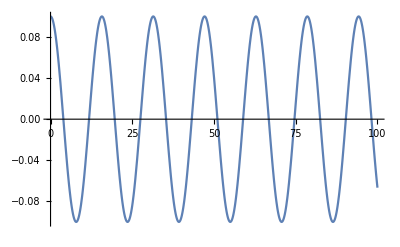

```mathematica
eq = {r''[t] + 0.16r[t] == 0}
bc = {r[0] == 0.1, r'[0] == 0}

nSol = 
NDSolve[
Join[eq,bc],
r[t],
{t, 0 ,100}]

Plot[
r[t] /. nSol,
{t, 0, 100},
PlotRange->All]
```

{0.16 r[t]+0.1 r'[t]+r''[t]==0}

{{r[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

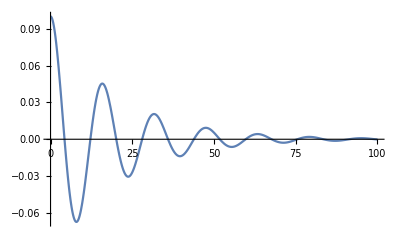

```mathematica
eq2=  {r''[t] + 0.1r'[t] + 0.16r[t] == 0}

nSol2 = 
NDSolve[
Join[eq2, bc],
r[t],
{t, 0, 100}]

Plot[
r[t] /. nSol2,
{t, 0, 100},
PlotRange->All]
```

### Question 4

```mathematica
D[Sin[i] + Cos[i]^2, i]
```

Cos[i]-2 Cos[i] Sin[i]

```mathematica
M = 201
x = Table[(j-1)(2 π/(M-1)), {j, 1, M}];
f = Table[Sin[i] + Cos[i]^2, {i, x}] ;

f' = Table[Cos[i]-2 Cos[i] Sin[i], {i, x}];

x //N
f // N
f' // N
```

201

{0.,0.0314159,0.0628319,0.0942478,0.125664,0.15708,0.188496,0.219911,0.251327,0.282743,0.314159,0.345575,0.376991,0.408407,0.439823,0.471239,0.502655,0.534071,0.565487,0.596903,0.628319,0.659734,0.69115,0.722566,0.753982,0.785398,0.816814,0.84823,0.879646,0.911062,0.942478,0.973894,1.00531,1.03673,1.06814,1.09956,1.13097,1.16239,1.19381,1.22522,1.25664,1.28805,1.31947,1.35088,1.3823,1.41372,1.44513,1.47655,1.50796,1.53938,1.5708,1.60221,1.63363,1.66504,1.69646,1.72788,1.75929,1.79071,1.82212,1.85354,1.88496,1.91637,1.94779,1.9792,2.01062,2.04204,2.07345,2.10487,2.13628,2.1677,2.19911,2.23053,2.26195,2.29336,2.32478,2.35619,2.38761,2.41903,2.45044,2.48186,2.51327,2.54469,2.57611,2.60752,2.63894,2.67035,2.70177,2.73319,2.7646,2.79602,2.82743,2.85885,2.89027,2.92168,2.9531,2.98451,3.01593,3.04734,3.07876,3.11018,3.14159,3.17301,3.20442,3.23584,3.26726,3.29867,3.33009,3.3615,3.39292,3.42434,3.45575,3.48717,3.51858,3.55,3.58142,3.61283,3.64425,3.67566,3.70708,3.7385,3.76991,3.80133,3.83274,3.86416,3.89557,3.92699,3.95841,3.98982,4.02124,4.05265,4.08407,4.11549,4.1469,4.17832,4.20973,4.24115,4.27257,4.30398,4.3354,4.36681,4.39823,4.42965,4.46106,4.49248,4.52389,4.55531,4.58673,4.61814,4.64956,4.68097,4.71239,4.7438,4.77522,4.80664,4.83805,4.86947,4.90088,4.9323,4.96372,4.99513,5.02655,5.05796,5.08938,5.1208,5.15221,5.18363,5.21504,5.24646,5.27788,5.30929,5.34071,5.37212,5.40354,5.43496,5.46637,5.49779,5.5292,5.56062,5.59203,5.62345,5.65487,5.68628,5.7177,5.74911,5.78053,5.81195,5.84336,5.87478,5.90619,5.93761,5.96903,6.00044,6.03186,6.06327,6.09469,6.12611,6.15752,6.18894,6.22035,6.25177,6.28319}

{1.,1.03042,1.05885,1.08525,1.10962,1.13196,1.15227,1.17056,1.18684,1.20116,1.21353,1.22399,1.23261,1.23942,1.24449,1.24788,1.24967,1.24992,1.24872,1.24615,1.24229,1.23725,1.23111,1.22398,1.21594,1.20711,1.19757,1.18744,1.17682,1.16581,1.15451,1.14302,1.13144,1.11987,1.10839,1.09711,1.08612,1.07548,1.06529,1.05562,1.04655,1.03813,1.03043,1.0235,1.0174,1.01216,1.00782,1.00442,1.00197,1.00049,1.,1.00049,1.00197,1.00442,1.00782,1.01216,1.0174,1.0235,1.03043,1.03813,1.04655,1.05562,1.06529,1.07548,1.08612,1.09711,1.10839,1.11987,1.13144,1.14302,1.15451,1.16581,1.17682,1.18744,1.19757,1.20711,1.21594,1.22398,1.23111,1.23725,1.24229,1.24615,1.24872,1.24992,1.24967,1.24788,1.24449,1.23942,1.23261,1.22399,1.21353,1.20116,1.18684,1.17056,1.15227,1.13196,1.10962,1.08525,1.05885,1.03042,1.,0.967603,0.933267,0.897035,0.858958,0.819094,0.777507,0.73427,0.689463,0.643173,0.595492,0.546519,0.49636,0.445126,0.392933,0.339902,0.28616,0.231835,0.177063,0.121979,0.0667232,0.0114379,-0.0437333,-0.0986452,-0.153152,-0.207107,-0.260364,-0.312778,-0.364204,-0.4145,-0.463525,-0.511143,-0.557218,-0.601619,-0.64422,-0.684899,-0.723539,-0.760028,-0.794261,-0.826137,-0.855565,-0.882458,-0.906737,-0.92833,-0.947175,-0.963217,-0.976406,-0.986706,-0.994084,-0.99852,-1.,-0.99852,-0.994084,-0.986706,-0.976406,-0.963217,-0.947175,-0.92833,-0.906737,-0.882458,-0.855565,-0.826137,-0.794261,-0.760028,-0.723539,-0.684899,-0.64422,-0.601619,-0.557218,-0.511143,-0.463525,-0.4145,-0.364204,-0.312778,-0.260364,-0.207107,-0.153152,-0.0986452,-0.0437333,0.0114379,0.0667232,0.121979,0.177063,0.231835,0.28616,0.339902,0.392933,0.445126,0.49636,0.546519,0.595492,0.643173,0.689463,0.73427,0.777507,0.819094,0.858958,0.897035,0.933267,0.967603,1.}

{1.,0.936716,0.872693,0.808181,0.743425,0.678671,0.614163,0.550137,0.486829,0.424467,0.363271,0.303457,0.245229,0.188786,0.134314,0.0819895,0.0319788,-0.0155647,-0.0604991,-0.102696,-0.14204,-0.178428,-0.211774,-0.242004,-0.269058,-0.292893,-0.31348,-0.330803,-0.344863,-0.355676,-0.363271,-0.367693,-0.369,-0.367265,-0.362574,-0.355026,-0.344734,-0.331821,-0.316423,-0.298686,-0.278768,-0.256836,-0.233064,-0.207636,-0.180743,-0.152583,-0.123357,-0.093273,-0.0625427,-0.0313798,0.,0.0313798,0.0625427,0.093273,0.123357,0.152583,0.180743,0.207636,0.233064,0.256836,0.278768,0.298686,0.316423,0.331821,0.344734,0.355026,0.362574,0.367265,0.369,0.367693,0.363271,0.355676,0.344863,0.330803,0.31348,0.292893,0.269058,0.242004,0.211774,0.178428,0.14204,0.102696,0.0604991,0.0155647,-0.0319788,-0.0819895,-0.134314,-0.188786,-0.245229,-0.303457,-0.363271,-0.424467,-0.486829,-0.550137,-0.614163,-0.678671,-0.743425,-0.808181,-0.872693,-0.936716,-1.,-1.0623,-1.12336,-1.18294,-1.2408,-1.29671,-1.35041,-1.4017,-1.45034,-1.49612,-1.53884,-1.5783,-1.61432,-1.64672,-1.67534,-1.70002,-1.72063,-1.73705,-1.74915,-1.75686,-1.76007,-1.75874,-1.7528,-1.74223,-1.727,-1.70711,-1.68257,-1.65343,-1.61971,-1.58149,-1.53884,-1.49186,-1.44065,-1.38535,-1.32608,-1.26301,-1.19629,-1.12612,-1.05267,-0.976162,-0.896802,-0.814818,-0.730444,-0.643923,-0.555506,-0.465451,-0.374023,-0.28149,-0.188124,-0.0942013,0.,0.0942013,0.188124,0.28149,0.374023,0.465451,0.555506,0.643923,0.730444,0.814818,0.896802,0.976162,1.05267,1.12612,1.19629,1.26301,1.32608,1.38535,1.44065,1.49186,1.53884,1.58149,1.61971,1.65343,1.68257,1.70711,1.727,1.74223,1.7528,1.75874,1.76007,1.75686,1.74915,1.73705,1.72063,1.70002,1.67534,1.64672,1.61432,1.5783,1.53884,1.49612,1.45034,1.4017,1.35041,1.29671,1.2408,1.18294,1.12336,1.0623,1.}

```mathematica
h = (2 π/(M-1))
```

π/100

```mathematica
center[list_] :=
(Sin[RotateLeft[list]] + Cos[RotateLeft[list]]^2 - Sin[RotateRight[list]] - Cos[RotateRight[list]]^2)/(2h)
```

```mathematica
center[x[[2;;-2]]] //N
```

{1.45221,0.872612,0.80814,0.743425,0.678712,0.614243,0.550257,0.486987,0.424661,0.363502,0.303721,0.245527,0.189115,0.134672,0.0823752,0.0323901,-0.0151298,-0.0600428,-0.10222,-0.141547,-0.177921,-0.211255,-0.241474,-0.268521,-0.292352,-0.312936,-0.330259,-0.344322,-0.35514,-0.362742,-0.367174,-0.368493,-0.366773,-0.362098,-0.354569,-0.344297,-0.331407,-0.316033,-0.298322,-0.278432,-0.256529,-0.232788,-0.207392,-0.180532,-0.152405,-0.123214,-0.0931652,-0.0624706,-0.0313436,0.,0.0313436,0.0624706,0.0931652,0.123214,0.152405,0.180532,0.207392,0.232788,0.256529,0.278432,0.298322,0.316033,0.331407,0.344297,0.354569,0.362098,0.366773,0.368493,0.367174,0.362742,0.35514,0.344322,0.330259,0.312936,0.292352,0.268521,0.241474,0.211255,0.177921,0.141547,0.10222,0.0600428,0.0151298,-0.0323901,-0.0823752,-0.134672,-0.189115,-0.245527,-0.303721,-0.363502,-0.424661,-0.486987,-0.550257,-0.614243,-0.678712,-0.743425,-0.80814,-0.872612,-0.936593,-0.999836,-1.06209,-1.12311,-1.18266,-1.24048,-1.29634,-1.35001,-1.40126,-1.44986,-1.49561,-1.5383,-1.57773,-1.61372,-1.64609,-1.67468,-1.69934,-1.71994,-1.73633,-1.74842,-1.75611,-1.75931,-1.75797,-1.75203,-1.74145,-1.72622,-1.70633,-1.6818,-1.65267,-1.61896,-1.58075,-1.53812,-1.49116,-1.43997,-1.38469,-1.32545,-1.2624,-1.19572,-1.12557,-1.05216,-0.975687,-0.896365,-0.81442,-0.730086,-0.643607,-0.555233,-0.465222,-0.373839,-0.281351,-0.188031,-0.0941548,0.,0.0941548,0.188031,0.281351,0.373839,0.465222,0.555233,0.643607,0.730086,0.81442,0.896365,0.975687,1.05216,1.12557,1.19572,1.2624,1.32545,1.38469,1.43997,1.49116,1.53812,1.58075,1.61896,1.65267,1.6818,1.70633,1.72622,1.74145,1.75203,1.75797,1.75931,1.75611,1.74842,1.73633,1.71994,1.69934,1.67468,1.64609,1.61372,1.57773,1.5383,1.49561,1.44986,1.40126,1.35001,1.29634,1.24048,1.18266,1.12311,1.54631}

```mathematica
forward[list_] := 
(Sin[RotateLeft[list]] + Cos[RotateLeft[list]]^2 - Sin[list] - Cos[list]^2)/h
```

```mathematica
forward[x[[2;;-2]]] //N
```

{0.904756,0.840468,0.775813,0.711038,0.646387,0.5821,0.518414,0.45556,0.393763,0.33324,0.274202,0.216851,0.161378,0.107966,0.0567848,0.00799535,-0.0382549,-0.0818307,-0.12261,-0.160484,-0.195358,-0.227151,-0.255798,-0.281245,-0.303458,-0.322413,-0.338105,-0.350539,-0.35974,-0.365744,-0.368603,-0.368383,-0.365162,-0.359034,-0.350104,-0.33849,-0.324323,-0.307743,-0.288902,-0.267963,-0.245095,-0.22048,-0.194304,-0.16676,-0.13805,-0.108378,-0.0779529,-0.0469883,-0.0156989,0.0156989,0.0469883,0.0779529,0.108378,0.13805,0.16676,0.194304,0.22048,0.245095,0.267963,0.288902,0.307743,0.324323,0.33849,0.350104,0.359034,0.365162,0.368383,0.368603,0.365744,0.35974,0.350539,0.338105,0.322413,0.303458,0.281245,0.255798,0.227151,0.195358,0.160484,0.12261,0.0818307,0.0382549,-0.00799535,-0.0567848,-0.107966,-0.161378,-0.216851,-0.274202,-0.33324,-0.393763,-0.45556,-0.518414,-0.5821,-0.646387,-0.711038,-0.775813,-0.840468,-0.904756,-0.96843,-1.03124,-1.09294,-1.15329,-1.21203,-1.26893,-1.32375,-1.37627,-1.42625,-1.47348,-1.51774,-1.55885,-1.59661,-1.63083,-1.66135,-1.68802,-1.71067,-1.7292,-1.74347,-1.75338,-1.75884,-1.75979,-1.75615,-1.7479,-1.735,-1.71744,-1.69523,-1.66838,-1.63695,-1.60097,-1.56053,-1.51571,-1.4666,-1.41334,-1.35604,-1.29486,-1.22995,-1.16149,-1.08966,-1.01466,-0.93671,-0.856019,-0.77282,-0.687352,-0.599862,-0.510604,-0.419841,-0.327837,-0.234865,-0.141197,-0.0471123,0.0471123,0.141197,0.234865,0.327837,0.419841,0.510604,0.599862,0.687352,0.77282,0.856019,0.93671,1.01466,1.08966,1.16149,1.22995,1.29486,1.35604,1.41334,1.4666,1.51571,1.56053,1.60097,1.63695,1.66838,1.69523,1.71744,1.735,1.7479,1.75615,1.75979,1.75884,1.75338,1.74347,1.7292,1.71067,1.68802,1.66135,1.63083,1.59661,1.55885,1.51774,1.47348,1.42625,1.37627,1.32375,1.26893,1.21203,1.15329,1.09294,1.99967}

```mathematica
centered = center[x[[2;;-2]]];
forwarded = forward[x[[2;;-2]]];
```

```mathematica
centDiff = Abs[f'[[2;;-2]]-centered]
forDiff = Abs[f'[[2;;-2]] - forwarded]
```

{-Cos[π/100]+2 Cos[π/100] Sin[π/100]+(50 (-Cos[π/100]^2+Cos[π/50]^2+Sin[π/100]+Sin[π/50]))/π,197,-Cos[π/100]-2 Cos[π/100] Sin[π/100]+(50 (Cos[π/100]^2-Cos[π/50]^2+Sin[π/100]+Sin[π/50]))/π}
 |  |  |  |

{Cos[π/100]-2 Cos[π/100] Sin[π/100]-(100 (-Cos[π/100]^2+Cos[π/50]^2-Sin[π/100]+Sin[π/50]))/π,Cos[π/50]-2 Cos[π/50] Sin[π/50]-(100 (-Cos[π/50]^2+Cos[(3 π)/100]^2-Sin[π/50]+Sin[(3 π)/100]))/π,195,Cos[π/50]+2 Cos[π/50] Sin[π/50]-(100 (Cos[π/100]^2-Cos[π/50]^2-Sin[π/100]+Sin[π/50]))/π,-Cos[π/100]+(200 Sin[π/100])/π-2 Cos[π/100] Sin[π/100]}
 |  |  |  |

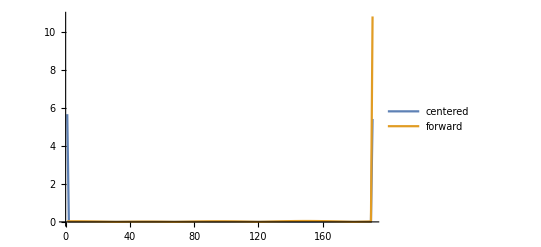

```mathematica
ListPlot[{centDiff, forDiff}, PlotRange->All, PlotLegends->{"centered", "forward"}, Joined->True]
```

centered

### Question 5

```mathematica
Fc[n_] := 1/2 n Cos[π n/2]^2+1/2(3n+1)Sin[(π n)/2]^2
```

```mathematica
Sn[1,j_] := j
Sn[n_,j_]  := Fc[Sn[n-1,j]]
```

```mathematica
Sn[1,5]
```

5

```mathematica
First[Position[Table[Sn[i,10], {i, 1, 10}],1]][[1]]
```

6

```mathematica
Table[Sn[i,2], {i, 1,2}]
```

{2,1}

```mathematica
Clear[l]
l[j_] :=
Module[
{ll,i},
ll = {};
i  = 1;
While[
Sn[i,j]≠   1,
AppendTo[ll, Sn[i,j]];i++];
i++]
```

```mathematica
l[6]
```

7

```mathematica
Max[l /@ Range[1000]]
```

114

```mathematica
Select[Range[1000], l[#] == 114 &]
```

{871}

### Question 6

```mathematica
upd[{a_,b_,c_}] := 1

upd[{a_,b_,c_}] := 0 /; OddQ[a+b+c]
```

```mathematica
function[list_]:=
upd /@ListConvolve[
{1,1,1},
list,1,0,Times,List]
```

```mathematica
ListDensityPlot[NestList[function, {0,0,0,0,1,0,0,0,0}, 100]]
```

## Section B

### Question 7

```mathematica
ρ[x_,y_] := ρ0 /; (x^2+y^2) ≤ a^2
ρ[x_,y_] := 0 /; (x^2+y^2) > a^2

V[x_,y_] := π ρ0 (x^2+y^2+a^2(Log[a^2]-1)) /; (x^2+y^2) ≤ a^2
V[x_,y_] := 2π ρ0 a^2 Log[Sqrt[x^2+y^2]] /; (x^2+y^2) > a^2
```

```mathematica
ρ0 = 1
a = 1
Δ = 1
grid = Table[3, {i, 1,51}, {j, 1, 51}];

Do[grid[[1,j]] = V[1,j];grid[[51,j]] = V[51,j], {j, 1, 51}];
Do[grid[[i, 1]] = V[i, 1]; grid[[i, 51]] = V[i, 51], {i, 1, 51}];
```

1

1

1

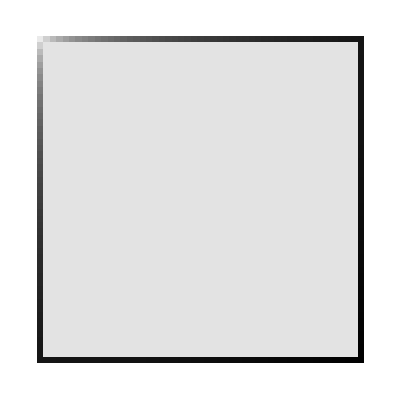

```mathematica
ArrayPlot[grid]
```

```mathematica
upd[list_] := 
Module[
{ll},
ll = list;

Do[
ll[[i,j]] = (list[[i+1,j]] + list[[i-1,j]] + list[[i,j+1]]+list[[i,j-1]])/4-Δ^2 π ρ[i,j],
{i, 2, 50}, {j, 2, 50}];
ll]
```

```mathematica
Do[
{prev, grid} = 
{
grid,
(RotateRight[grid] + RotateLeft[grid] + RotateRight /@ grid + RotateLeft /@ grid)/4-
```

```mathematica
Do[
{prev,mesh}=
{
mesh,
ϵ (RotateRight[mesh]+RotateLeft[mesh]+RotateRight/@mesh+RotateLeft/@mesh)+(2-4 ϵ) mesh-prev};bc[],{it,1,steps}]
```